```mathematica
GG = (Abs[a] y^(a p - 1) Exp[-(y / β)^a])/(β^(a p)Gamma[p])
```

(Abs[a] β^(-a p) y^(a p-1) ⅇ^(-(y/β)^a))/p

```mathematica
TeXForm[GG]
```

\frac{\left| a\right|  \beta ^{-a p} y^{a p-1} e^{-\left(\frac{y}{\beta
   }\right)^a}}{\Gamma (p)}

```mathematica
Sum[GG/.y->yi, {yi ,1, 5}]
```

(Abs[a] ⅇ^(-(1/β)^a) β^(-a p))/p+(Abs[a] ⅇ^(-2^a (1/β)^a) 2^(a p-1) β^(-a p))/p+(Abs[a] ⅇ^(-3^a (1/β)^a) 3^(a p-1) β^(-a p))/p+(Abs[a] ⅇ^(-4^a (1/β)^a) 4^(a p-1) β^(-a p))/p+(Abs[a] ⅇ^(-5^a (1/β)^a) 5^(a p-1) β^(-a p))/p

```mathematica
Product[GG, {i, 1, 5}]
```

(Abs[a]^5 β^(-5 a p) y^(5 a p-5) ⅇ^(-5 (y/β)^a))/p^5

-((x1-x2-1) (x1+x2))/(2 β)

```mathematica
mGA = 1/(1 - β t/n)^n
```

(1-(β t)/n)^-n

```mathematica
Log[mGA]//Simplify
```

log((1-(β t)/n)^-n)

```mathematica
Log[(1 - β t/n)^n]
```

log((1-(β t)/n)^n)

```mathematica
D[-n * Log[1 - β t / n], {β, 1}]/.t->0
```

0

```mathematica
c1 = D[CumulantGeneratingFunction[GammaDistribution[n, β/n], t], {t, 1}]/.t->0
c2 =D[CumulantGeneratingFunction[GammaDistribution[n, β/n], t], {t, 2}]/.t->0
c3 = D[CumulantGeneratingFunction[GammaDistribution[n, β/n], t], {t, 3}]/.t->0
c4 = D[CumulantGeneratingFunction[GammaDistribution[n, β/n], t], {t, 4}]/.t->0
```

β

β^2/n

(2 β^3)/n^2

(6 β^4)/n^3

```mathematica
TeXForm[c3]
TeXForm[c4]
```

\frac{6 \beta ^4}{n^3}

```mathematica
c4 / c2^2
```

6/n

```mathematica
gb2 = (Abs[a] q (y/b)^(a - 1))/(b (1 + (y/b)^a)^(q + 1))
```

(q Abs[a] (y/b)^(a-1) ((y/b)^a+1)^(-q-1))/b

```mathematica
GB2 = 1 - (1/(1+(y/b)^2))^q
```

1-(1/(y^2/b^2+1))^q

```mathematica
gb2h = gb2/(1 - GB2)
```

(q Abs[a] (y/b)^(a-1) (1/(y^2/b^2+1))^-q ((y/b)^a+1)^(-q-1))/b

```mathematica
Manipulate[Plot[gb2h/.{a->a1, b->b1, q->q1},{y, 0, 4}, PlotRange->{0, 5}], {a1, 0, 2}, {b1, 1, 2}, {q1, 0, 2}]
```

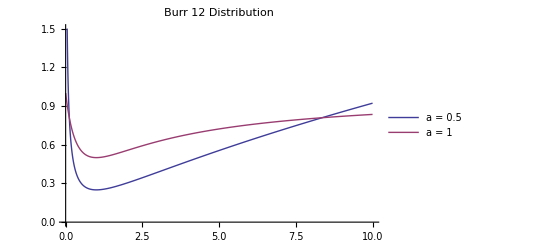

/Users/spencerlyon2/Documents/School/BYUclasses/Economics/E588/Homework/HW2/Graphics/b12Haz.pdf

```mathematica
burr12Ha = Plot[{gb2h/.{b->1, q -> 1, a->.5}, gb2h/.{b->1, q -> 1, a->1.0}}, {y, 0, 10}, PlotRange->{0, 1.5}, PlotLegends->{"a = 0.5", "a = 1"}, PlotLabel->"Burr 12 Distribution"]
Export["/Users/spencerlyon2/Documents/School/BYUclasses/Economics/E588/Homework/HW2/Graphics/b12Haz.pdf", burr12Ha]
```

```mathematica
Manipulate[Plot[HazardFunction[WeibullDistribution[p1, p2],x],{x,-1,5},Filling->Axis, PlotRange->{0, 4}, PlotLabel->"Weibull Hazard"], {p1, 0, 3},  {p2, 0, 3}]
Manipulate[Plot[HazardFunction[GammaDistribution[p1, p2],x],{x,-1,5},Filling->Axis, PlotRange->{0, 4}, PlotLabel->"Gamma Hazard"], {p1, 0, 3},  {p2, 0, 3}]
Manipulate[Plot[HazardFunction[ExponentialDistribution[p1],x],{x,-1,5},Filling->Axis, PlotRange->{0, 4}, PlotLabel->"Exponential Hazard"], {p1, 0, 3}]
```

```mathematica
PDF[LogNormalDistribution[μ, σ], x]
```

Piecewise[{{(ⅇ^(-(log(x)-μ)^2/(2 σ^2)))/(√(2 π) σ x), x>0}, {0, True}}]

```mathematica
PDF[NormalDistribution[μ, σ], x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Export["/Users/spencerlyon2/Documents/School/BYUclasses/Economics/E588/Homework/HW2/Graphics/b12Haz.pdf", burr12Ha]
```

/Users/spencerlyon2/Documents/School/BYUclasses/Economics/E588/Homework/HW2/Graphics/b12Haz.pdf

```mathematica
f = Sin[x]
```

sin(x)

```mathematica
case1 = gb2h /.{a->5, b->1, q->1}
```

(5 y^4 (y^2+1))/((y^5+1)^2)

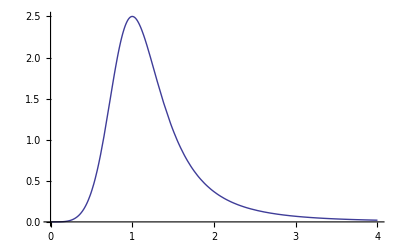

```mathematica
Plot[case1, {y,0, 4}]
```

```mathematica
TeXForm[gb2h]
```

\frac{q \left| a\right|  \left(\frac{y}{b}\right)^{a-1}
   \left(\frac{1}{\frac{y^2}{b^2}+1}\right)^{-q}
   \left(\left(\frac{y}{b}\right)^a+1\right)^{-q-1}}{b}

```mathematica
1/(2 √z)PDF[LogNormalDistribution[μ, σ], √z]//FullSimplify
```

Piecewise[{{(ⅇ^(-(log(z)-2 μ)^2/(8 σ^2)))/(2 √(2 π) σ z), √z>0}, {0, True}}]

```mathematica
PDF[LogNormalDistribution[μ, σ], z]
```

Piecewise[{{(ⅇ^(-(log(z)-μ)^2/(2 σ^2)))/(√(2 π) σ z), z>0}, {0, True}}]

```mathematica
PDF[LogNormalDistribution[2μ, 2σ], z]
```

Piecewise[{{(ⅇ^(-(log(z)-2 μ)^2/(8 σ^2)))/(2 √(2 π) σ z), z>0}, {0, True}}]

```mathematica
D[(y/β)^a, y] PDF[GammaDistribution[p, 1], (y/β)^a]//FullSimplify//TeXForm
```

\begin{cases}
 \frac{a e^{-\left(\frac{y}{\beta }\right)^a} \left(\left(\frac{y}{\beta
   }\right)^a\right)^p}{y \Gamma (p)} & \left(\frac{y}{\beta }\right)^a>0 \\
 0 & \text{True}
\end{cases}

```mathematica
D[(y/β)^a, y]
```

(a (y/β)^(a-1))/β

```mathematica
cN = CumulantGeneratingFunction[NormalDistribution[μ, σ], t]
```

(σ^2 t^2)/2+μ t

```mathematica
Kurtosis[NormalDistribution[μ, σ]]
```

3

```mathematica
({{2, 2}, {2, 5/2}}).Piecewise[{{4,, 3}}}]
```

```mathematica
D[Exp[-1/2(y Σ y - y Σ μ)], y]
```

1/2 ⅇ^(1/2 (μ Σ y-Σ y^2)) (μ Σ-2 Σ y)

```mathematica
{{2,2},{2,5/2}}
```

(2 | 2
2 | 5/2)

```mathematica
{{2,2},{2,5/2}}.{{Subscript[x, 1]}, {Subscript[x, 2]}}//TeXForm
```

\left(
\begin{array}{c}
 2 x_1+2 x_2 \\
 2 x_1+\frac{5 x_2}{2} \\
\end{array}
\right)

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, 1], Subscript[μ, 2]}, Σ], {y1, y2}]
```

PDF[MultinormalDistribution[μ,Σ],{y1,y2}]

```mathematica
Table[{tt, D[cN, {t, tt}]}, {tt, 1, 4, 1}]
```

(1 | t σ^2+μ
2 | σ^2
3 | 0
4 | 0)

```mathematica
Inverse[2 * {{2,2},{2,5/2}}].{{-1},{-3}}
```

(7/4
-2)

```mathematica
Inverse[2 * {{2,2},{2,5/2}}]
```

(5/4 | -1
-1 | 1)

```mathematica
Eigensystem[({{4, 4}, {4, 5}})]
```

(1/2 (9+√65) | 1/2 (9-√65)
{1/8 (-1+√65),1} | {1/8 (-1-√65),1})

```mathematica
N[√65]
```

8.06226

```mathematica
i = Transpose[{1, 1, 1,1}]
```

Transpose[{1,1,1,1}]

```mathematica
Transpose[i].i//Expand
```

Transpose[(Transpose[{1,1,1,1}])].Transpose[{1,1,1,1}]

```mathematica
{1, 1, 1,1}.Transpose[{1, 1, 1,1}]
```

{1,1,1,1}.Transpose[{1,1,1,1}]